# Motion of a classical particle in a box

Free classical particle moving around in a box

AnimationRunning has been set to False

## We will make an animated picture of our particle moving around inside a box before collision with the walls

The first step is to create a box and a point with given coordinates withing the box

Make a Raster:

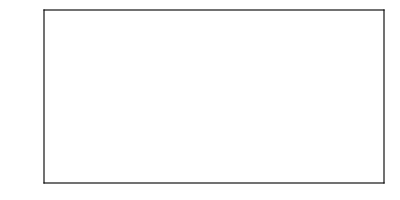

```mathematica
mybox[mx_Integer,ny_Integer]:=Graphics[Raster[ConstantArray[1,{ny,mx}]],Frame->True,FrameTicks->None];
mybox[20,10]
```

Make a Raster with a dot:

```mathematica
mybox[{mx_Integer,ny_Integer},{px_Integer,qy_Integer}]:=Graphics[Raster[ReplacePart[ConstantArray[{1,1,1},{ny,mx}],{qy,px}->{1,0,0}]],Frame->True,FrameTicks->None];
mybox[{20,10},{5,5}]
```

-Graphics-

Make a simple animation of this before collisions with a wall:

```mathematica
Animate[mybox[{20,10},{u,v}],{u,5,8,1},{v,5,8,1},AnimationRunning->False]
```

Build the above into a single function:

```mathematica
myAnimatedbox[{mx_Integer,ny_Integer},{x0_Integer,y0_Integer},{vx_Integer,vy_Integer}]:=Animate[mybox[{mx,ny},{u,v}],{u,x0,mx,vx},{v,y0,ny,vy},AnimationRunning->False];
myAnimatedbox[{20,10},{5,5},{1,1}]
```

Make the animated box more uniform using a single parameter (time):

```mathematica
mytimeAnimatedbox[{mx_Integer,ny_Integer},{x0_Integer,y0_Integer},{vx_Integer,vy_Integer}]:=Animate[mybox[{mx,ny},{x0 + vx t,y0 + vy t}],{t,0,Min[(mx-x0)/vx,(ny-y0)/vy],1},AnimationRunning->False];
mytimeAnimatedbox[{20,10},{5,5},{1,1}]
```

## What happens after collision with a wall?

We can treat the x and y directions independently (need one function for both directions)

What happens after the n^th time step in one direction?

If the n^th time step involves a collision with the wall, then the particle’s velocity in the direction of that collision simply changes sign. We will use this idea to construct the position of the particle after the n^th step.

The function that defines the position after n steps is:

```mathematica
posn[pos_Integer,v_Integer,posmax_Integer,t_Integer]:=1+If[EvenQ[Floor[(pos+v (t-1))/(posmax-1)]],Mod[pos + v (t-1),posmax-1],(posmax-1)Floor[(pos+v (t-1))/(posmax-1)+1]-pos-v (t-1)];
```

After the n^th time step the position in one direction looks like:

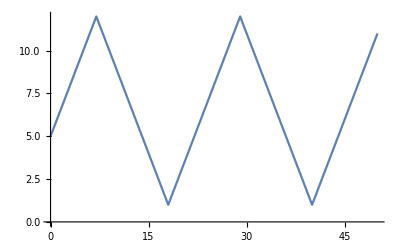

```mathematica
ListLinePlot[Table[{n,posn[5,1,12,n]},{n,0,50}]]
```

Implement this in the animated box (both x and y directions):

```mathematica
myimprovedtimeAnimatedbox[{mx_Integer,ny_Integer},{x0_Integer,y0_Integer},{vx_Integer,vy_Integer}]:=Animate[mybox[{mx,ny},{posn[x0,vx,mx,t],posn[y0,vy,ny,t]}],{t,0,Min[(mx-x0)/vx,(ny-y0)/vy],1},AnimationRunning->False];
```

Same as previous answer since time restriction still present:

```mathematica
myimprovedtimeAnimatedbox[{20,10},{5,5},{1,1}]
```

Lift the time limitations on the animation:

```mathematica
myFinalbox[{m_Integer,n_Integer},{x_Integer,y_Integer},{vx_Integer,vy_Integer},tt_Integer]:=Animate[mybox[{m,n},{posn[x,vx,m,t],posn[y,vy,n,t]}],{t,0,tt,1},AnimationRepetitions->1];
```

```mathematica
myFinalbox[{60,40},{35,5},{1,1},600]
```

Let us slow down the animation for better visual effects:

```mathematica
myFinalAnimatedbox[{m_Integer,n_Integer},{x_Integer,y_Integer},{vx_Integer,vy_Integer},tt_Integer]:=Animate[mybox[{m,n},{f[x,vx,m,t],f[y,vy,n,t]}],{t,0,tt,1},AnimationRate->20,AnimationRunning->True];
```

```mathematica
myFinalAnimatedbox[{60,40},{35,5},{1,1},600]
```

## Examples of the final animated graphics

Here is an example of an animated final result:

Size of this box:  60 x 40
Initial conditions:  Position ->  25, 7;  Velocity -> 2,1;  Total number of time steps -> 600;

```mathematica
myFinalAnimatedbox[{60,40},{25,7},{2,1},600]
```

## Can we make this work in 3 dimensions?

The first step is again to create a box and a point with given coordinates withing the box. This time we need a 3D box

Make a 3D Raster:

```mathematica
my3Dbox[mx_Integer,ny_Integer,oz_Integer]:=Graphics3D[Raster3D[ConstantArray[{1,1,1,0},{ny,mx,oz}]]];
my3Dbox[20,10, 5]
```

-Graphics3D-

Make a 3D Raster with a dot:

```mathematica
my3Dbox[{mx_Integer,ny_Integer,oz_Integer},{px_Integer,qy_Integer,rz_Integer}]:=Graphics3D[Raster3D[ReplacePart[ConstantArray[{1,1,1,0},{ny,mx,oz}],{qy,px,rz}->{1,0,0,1}]]];
my3Dbox[{20,10,5},{5,5,4}]
```

-Graphics3D-

Make the animated box more uniform using a single parameter (time):

```mathematica
my3DtimeAnimatedbox[{mx_Integer,ny_Integer,oz_Integer},{x0_Integer,y0_Integer,z0_Integer},{vx_Integer,vy_Integer,vz_Integer}]:=Animate[my3Dbox[{mx,ny,oz},{x0+vx t,y0+vy t,z0+vz t}],{t,0,Min[(mx-x0)/vx,(ny-y0)/vy,(oz-z0)/vz],1},AnimationRunning->False];
```

```mathematica
my3DtimeAnimatedbox[{20,10,5},{2,2,1},{1,1,1}]
```

After collision with the walls:

```mathematica
my3DFinalbox[{m_Integer,n_Integer,o_Integer},{x_Integer,y_Integer,z_Integer},{vx_Integer,vy_Integer,vz_Integer},tt_Integer]:=Animate[my3Dbox[{m,n,o},{f[x,vx,m,t],f[y,vy,n,t],f[z,vz,o,t]}],{t,0,tt,1},AnimationRate->5,AnimationRunning->True];
```

```mathematica
my3DFinalbox[{20,10,5},{2,2,1},{1,1,1},100]
```

## Examples of the final animated graphics in 3D

Here is an example of an animated final result:

Size of this box:  10 x 10 x 10
Initial conditions:  Position ->  5, 5, 5;  Velocity -> 1,1,1;  Total number of time steps -> 50;

```mathematica
my3DFinalbox[{10,10,10},{5,5,5},{1,1,1},50]
```

Here is another example of an animated final result:

Size of this box:  10 x 10 x 10
Initial conditions:  Position ->  5, 5, 5;  Velocity -> 1,1,2;  Total number of time steps -> 50;

```mathematica
my3DFinalbox[{10,10,10},{5,5,5},{1,1,2},50]
```

## Ideas for things to do in the future (future explorations)

Starting from this set up one can set up more complicated visualizations. A few ideas are as follows:

Include a constant acceleration in one or more directions (such as gravity in one direction). This would replicate a more realistic situation. This could be implemented first in 2D and then again in 3D

Attach 2D rasters to the faces of the 3D raster. At each collision make the appropriate elements of the 2D rasters light up showing a collision with the wall

Collisions with the walls can be made imperfect to find what effect that has on the final results

Authorship information

Bhubanjyoti Bhattacharya

June 20, 2017

bhujyo@gmail.com